```mathematica
ϕ1[n3_]:=1+(2*n3-n3^2+2*(1-n3)*Log[1-n3])/(3*n3)
ϕ2[n3_]:=1-(2*n3-3*n3^2+2*n3^3+2*(1-n3)^2*Log[1-n3])/(3*n3^2)
phi[n0_,n1_,n2_,n3_,n1v_,n2v_,nt1_,nt2_]:=-n0*Log[1-n3] + ϕ1[n3]*(n1*n2-n1v*n2v)/(1-n3) +ϕ2[n3]*((a+b)*n2^3-3*a*n2*n2v^2+3*a*n2v^2*nt2-3*b*n2*(2*nt1^2+nt2^2)+(2*b-a)*(2*nt1^3+nt2^3))/(24*Pi*(1-n3)^2)
f =η*Log[η]+Pi/6*σ^3*phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify
```

1/9 η ((η (9 (5-6 η+η^2)-8 a (1-3 η+η^2)-2 b (1-3 η+η^2)))/(-1+η)^2-(-9+8 a+2 b) Log[1-η]+9 Log[η])

```mathematica
p = -f + η*D[f,η]//Simplify;
mu = D[f-η*Log[η],η]//Simplify;
muCS=mu/.{a->3/2,b->-3/2};
mu-muCS//Simplify
z =Pi/6*σ^3*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify 
γ = Pi*σ^2*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify
χ = (η*D[mu+Log[η],η])^(-1)//Simplify
χCS=χ/.{a->3/2,b->-3/2}//Simplify
```

-((-9+8 a+2 b) (η (-1+7 η-6 η^2+2 η^3)+(-1+η)^3 Log[1-η]))/(9 (-1+η)^3)

1/9 ((η (9 (1-6 η+5 η^2)+8 a (-2+5 η-6 η^2+η^3)+2 b (-2+5 η-6 η^2+η^3)))/(-1+η)^3+2 (-9+8 a+2 b) Log[1-η])

(η (5-6 η+η^2-3 a (1-3 η+η^2)-2 b (1-3 η+η^2)))/(-1+η)^2-(-2+3 a+2 b) Log[1-η]

-(9 (-1+η)^4)/(-9-36 η-9 (-5+8 a+2 b) η^2+4 (-9+16 a+4 b) η^3-2 (-27+28 a+7 b) η^4+2 (-9+8 a+2 b) η^5)

(-1+η)^4/(1+4 η+4 η^2-4 η^3+η^4)

```mathematica
-1/9*(-9-36 η-9 (-5+8 a+2 b) η^2+4 (-9+16 a+4 b) η^3-2 (-27+28 a+7 b) η^4+2 (-9+8 a+2 b) η^5)-(1+4 η+4 η^2-4 η^3+η^4)//Simplify
```

-1/9 (-9+8 a+2 b) η^2 (-9+8 η-7 η^2+2 η^3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n0]//Simplify
```

-Log[1-n3]

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1]//Simplify
```

1/3 n2 ((-5+n3)/(-1+n3)+(2 Log[1-n3])/n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]//Simplify
```

1/(72 (-1+n3)^2 n3^2 π)(24 n1 (1-n3) n3 π (-((-5+n3) n3)-2 (-1+n3) Log[1-n3])-2 (3 (a+b) n2^2-3 a n2v^2-3 b (2 nt1^2+nt2^2)) (n3-3 n3^2+n3^3+(-1+n3)^2 Log[1-n3]))

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]//Simplify
```

-1/(72 (-1+n3)^3 n3^3 π)(72 n0 (-1+n3)^2 n3^3 π+2 (-1+n3)^2 (a (n2^3-3 n2 n2v^2-2 nt1^3+3 n2v^2 nt2-nt2^3)+b (n2^3-3 n2 (2 nt1^2+nt2^2)+2 (2 nt1^3+nt2^3))) (n3 (2+n3)+2 Log[1-n3])-24 (n1 n2-n1v n2v) (-1+n3)^2 n3 π (n3 (2+n3)+2 Log[1-n3])+24 (n1 n2-n1v n2v) (1-n3) n3^2 π (-((-5+n3) n3)-2 (-1+n3) Log[1-n3])-4 n3 ((a+b) n2^3-3 a n2 n2v^2+3 a n2v^2 nt2-3 b n2 (2 nt1^2+nt2^2)-(a-2 b) (2 nt1^3+nt2^3)) (n3-3 n3^2+n3^3+(-1+n3)^2 Log[1-n3]))

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1v]//Simplify
```

1/3 n2v ((5-n3)/(-1+n3)-(2 Log[1-n3])/n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2v]//Simplify
```

(n3 (a n2v (1-3 n3+n3^2) (n2-nt2)-2 n1v n3 (5-6 n3+n3^2) π)+(-1+n3)^2 (a n2v (n2-nt2)-4 n1v n3 π) Log[1-n3])/(6 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt1]//Simplify
```

(nt1 (2 b (n2-nt1)+a nt1) (n3 (1-3 n3+n3^2)+(-1+n3)^2 Log[1-n3]))/(6 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt2]//Simplify
```

-((2 b nt2 (-n2+nt2)+a (n2v^2-nt2^2)) (n3 (1-3 n3+n3^2)+(-1+n3)^2 Log[1-n3]))/(12 (-1+n3)^2 n3^2 π)

```mathematica
pCS=η*(1+η+η^2-η^3)/(1-η)^3//Simplify
```

(η (1+η+η^2-η^3))/(1-η)^3

```mathematica
p-pCS//Simplify
```

-((-9+8 a+2 b) η^3 (3-2 η+η^2))/(9 (-1+η)^3)

```mathematica
D[ϕ1[n3],n3]
```

(-2 n3-2 Log[1-n3])/(3 n3)-(2 n3-n3^2+2 (1-n3) Log[1-n3])/(3 n3^2)

```mathematica
D[ϕ2[n3],n3]
```

-(2-2 (1-n3)-6 n3+6 n3^2-4 (1-n3) Log[1-n3])/(3 n3^2)+(2 (2 n3-3 n3^2+2 n3^3+2 (1-n3)^2 Log[1-n3]))/(3 n3^3)

```mathematica
p-(η (-9-9 η-6 (-3+4 a+b) η^2+2 (4 a+b) η^3))/(9 (-1+η)^3)//Simplify
```

-((-9+8 a+2 b) η^4)/(9 (-1+η)^2)

```mathematica
p-(η (1+η+η^2-η^3))/(1-η)^3//Simplify
```

-((-9+8 a+2 b) η^3 (3-2 η+η^2))/(9 (-1+η)^3)

```mathematica
mu-(η (-8+9 η-3 η^2))/(-1+η)^3//Simplify
```

-((-9+8 a+2 b) (η (-1+7 η-6 η^2+2 η^3)+(-1+η)^3 Log[1-η]))/(9 (-1+η)^3)

```mathematica
p-z//Simplify
Series[p-z,{η,0,3}]//Simplify
```

-1/9 (-9+8 a+2 b) (η (2+η)+2 Log[1-η])

2/27 (-9+8 a+2 b) η^3+O[η]^4

```mathematica
pWBII[η_,a_,b_]:=-(η (9+9 η+6 (-3+4 a+b) η^2+(9-16 a-4 b) η^3+(-9+8 a+2 b) η^4))/(9 (-1+η)^3)
zWBII[η_,a_,b_]:=1/9 ((η (9 (1-6 η+5 η^2)+8 a (-2+5 η-6 η^2+η^3)+2 b (-2+5 η-6 η^2+η^3)))/(-1+η)^3+2 (-9+8 a+2 b) Log[1-η])
```

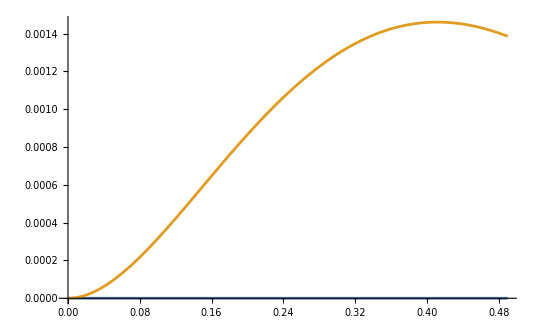

```mathematica
Plot[{(pWBII[e,1.5,-1.5]-zWBII[e,1.5,-1.5])/pWBII[e,1.5,-1.5],(pWBII[e,1.2,0]-zWBII[e,1.2,0])/pWBII[e,1.2,0]},{e,0.0,0.49}]
```